## Import Data from a series of Images

```mathematica
dir0="E:\\00_BelgianProject\\BelgianCells_April2023\\2023-06-07_RM734_April3mu_SHG_and_int\\2d40\\pol_dep_AH\\";
SetDirectory[dir0]
files=Drop[FileNames["*.png"],0];
CreateDirectory[dir0<>"\\0000_analisis"]
```

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\0000_analisis

#### Pick initial point for definition of measurement areas

```mathematica
(*careful, heigth and width interchanged :/ *)
img=Import@files[[10]];
heightarea=500/2;
widtharea=500/2;
{dC,dR}=ImageDimensions[img];
Manipulate[point=p;area={{dR-p[[2]]-widtharea,dR-p[[2]]+widtharea},{p[[1]]-heightarea,p[[1]]+heightarea}};Show[ImageAdjust[img,{0,2}],ImageTake[ImageAdjust[img,{0,2}],area[[1]],area[[2]]],ImageSize->500],{{p,{dR/2,dC/2}},Locator}]
```

```mathematica
initialArea=area
```

{{340.,840.},{773.,1273.}}

```mathematica
areaList=initialArea
point3=areaList
```

{{340.,840.},{773.,1273.}}

{{340.,840.},{773.,1273.}}

```mathematica
Det[point3]
```

-136800.

```mathematica
colorList=ColorData[24,"ColorList"]
colorList={colorList[[1]],colorList[[4]],colorList[[2]],colorList[[5]],colorList[[9]]}
rectangleList={EdgeForm[{Thickness[0.005],colorList[[1]]}],Opacity[0],Rectangle[{point3[[2,1]],dR-point3[[1,2]]},{point3[[2,2]],dR-point3[[1,1]]}]}
```

{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]}

{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765]}

{EdgeForm[{Thickness[0.005],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786]}],Opacity[0],Rectangle[{773.,360.},{1273.,860.}]}

```mathematica
img=Import@files[[9]];
ImagesAreas=Show[ImageAdjust[img,{0,2}],Graphics[rectangleList],ImageSize->500]
```

-Graphics-

```mathematica
files
```

{000.png,002.png,004.png,006.png,008.png,010.png,012.png,014.png,016.png,018.png,020.png,022.png,024.png,026.png,028.png,030.png,032.png,034.png,036.png,038.png,040.png,042.png,044.png,046.png,048.png,050.png,052.png,054.png,056.png,058.png,060.png,062.png,064.png,066.png,068.png,070.png,072.png,074.png,076.png,078.png,080.png,082.png,084.png,086.png,088.png,090.png,092.png,094.png,096.png,098.png,100.png,102.png,104.png,106.png,108.png,110.png,112.png,114.png,116.png,118.png,120.png,122.png,124.png,126.png,128.png,130.png,132.png,134.png,136.png,138.png,140.png,142.png,144.png,146.png,148.png,150.png,152.png,154.png,156.png,158.png,160.png,162.png,164.png,166.png,168.png,170.png,172.png,174.png,176.png,178.png,180.png}

```mathematica
angles=ToExpression@Table[StringTake[files[[i]],{1,StringPosition[files[[i]],".png"][[1,1]]-1}],{i,1,Length@files}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180}

```mathematica
nangles=Table[If[angles[[i]]+90>180,angles[[i]]+90-180,angles[[i]]+90],{i,1,Length@angles}]
```

{90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90}

```mathematica
angles=Flatten[ToExpression@StringCases[#,RegularExpression["seq_(\\d+)_2022"]->"$1"]&/@files]
```

```mathematica
ProgressIndicator[Dynamic[progress],{0,Length[files]}]
maxData={};
Do[
progress=i;
img=ColorConvert[Import[files[[i]]],"GrayScale"];
cropped=ImageAdjust[ImageTake[img, initialArea[[1]],initialArea[[2]]],{0,1}];
data=Map[{#,nangles[[i]]}&,ImageData[cropped],{2}];
If[Length[maxData]==0,maxData=data];
maxData=MapThread[
{Max[First[#1],First[#2]],If[First[#2]>First[#1],Last[#2],Last[#1]]}&,{maxData,data},2
],
{i,1,Length[files]}
]
```

```mathematica
int=Map[First[#]&,maxData,{2}];
```

```mathematica
Imax=Max[Quantile[int,0.99]]
normInt=int/Imax;
```

0.501961

```mathematica
plotIntensity=ArrayPlot[int,ColorFunction->"CherryTones",DataRange->{{0,145},{0,145}},
PlotRange->{All,All,{0,1}},
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0.]},
FrameLabel->{Style["x / μm",20],Style["y / μm",20]},
FrameTicksStyle->20,FrameTicks->{{{40,80,120},None},{{40,80,120},None}},
PlotLegends->Placed[BarLegend[
Range[0,1,.05],LegendMarkerSize->280,LegendMargins->0,LegendLabel->"I (a.u)",Ticks->Transpose[{Range[0,1,.2]}]
],{0.58,Above}]]
```

-Graphics-

```mathematica
plotIntensityNorm=ArrayPlot[normInt,ColorFunction->"CherryTones",DataRange->{{0,145},{0,145}},
PlotRange->{All,All,{0.0,1}},
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0.]},
FrameLabel->{Style["x / μm",20],Style["y / μm",20]},
FrameTicksStyle->20,FrameTicks->{{{40,80,120},None},{{40,80,120},None}},
PlotLegends->Placed[BarLegend[
Range[.0,1,.05],LegendMarkerSize->280,LegendMargins->0,LegendLabel->"I/Imax",Ticks->Transpose[{Range[.0,1,.2]}]
],{0.58,Above}]]
```

-Graphics-

```mathematica
angMax=Map[Last[#]&,maxData,{2}];
```

```mathematica
plotAngles=ArrayPlot[angMax,DataRange->{{0,145},{0,145}},
PlotRange->{All,All,{0,180}},
ColorFunction->"ThermometerColors",LabelStyle->{FontFamily->"Arial",18,GrayLevel[0.]},FrameLabel->{Style["x / μm",20],Style["y / μm",20]},FrameTicksStyle->20,FrameTicks->{{{40,80,120},None},{{40,80,120},None}},
PlotLegends->Placed[BarLegend[
Range[0,180,5],LegendMarkerSize->300,LegendMargins->0,LegendLabel->"ϕ (deg)",Ticks->Transpose[{Range[0,180,20]}]
],{0.58,Above}]
]
```

-Graphics-

```mathematica
profile=Table[angMax[[10,ii]],{ii,1,Dimensions[angMax][[1]]}];
profile2=Table[angMax[[ii,10]],{ii,1,Dimensions[angMax][[1]]}];
profile3=Table[angMax[[100,ii]],{ii,1,Dimensions[angMax][[1]]}];
profile4=Table[angMax[[ii,60]],{ii,1,Dimensions[angMax][[1]]}];
```

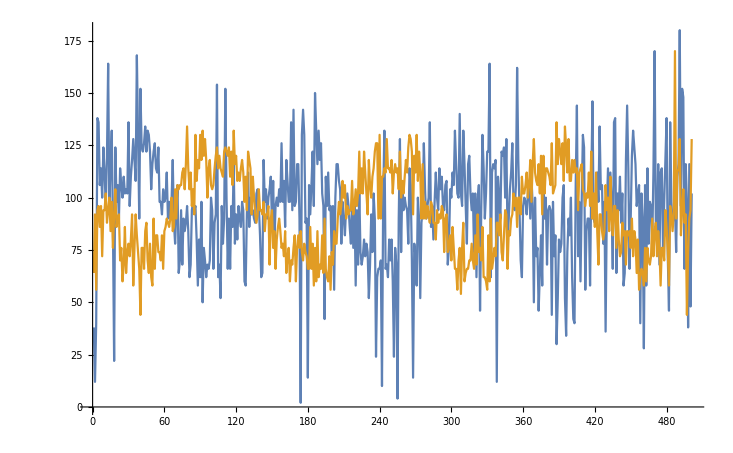

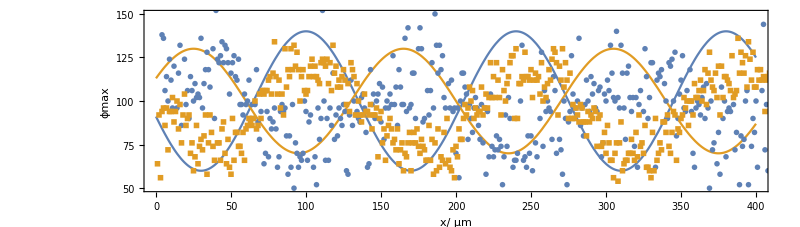

```mathematica
ListPlot[{profile,profile3},Joined->True]
angleProfile=Show[{Plot[{40Sin[2*Pi*(x-65)/140]+100,30Sin[-2*Pi*(x-60)/140]+100},{x,0,400},PlotRange->{{0,400},{50,150}}],ListPlot[{profile,profile3},Joined->{False,False},PlotMarkers->{Automatic,Scaled[0.025]}]},
Frame->True,AspectRatio->1/3.5,LabelStyle->Directive[22,Black],ImageSize->800,FrameLabel->{Style["x/ μm ",22,GrayLevel[0]],Style["ϕmax",22,GrayLevel[0]]}
]
```

```mathematica
Export[dir0<>"\\angleProfile.png",angleProfile,ImageResolution->300]
```

E:\00_BelgianProject\BelgianCells_December2021\RM734_BelgianCells_Dec21_576mu_SHG\2D4040\0000_analisis\\angleProfile.png

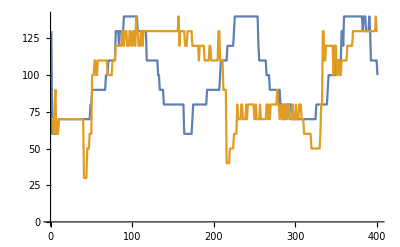

```mathematica
ListPlot[{profile,profile2},Joined->True]
```

```mathematica
Export[dir0<>"\\Image_Areas.png",ImagesAreas,ImageResolution->300]
Export[dir0<>"\\angleProfile2.png",plotAngles,ImageResolution->600]
Export[dir0<>"\\angleProfile2.svg",plotAngles,ImageResolution->300]
Export[dir0<>"\\intensityProfile.svg",plotIntensity,ImageResolution->300]
Export[dir0<>"\\intensityProfile.png",plotIntensity,ImageResolution->600]
Export[dir0<>"\\intensityProfileNorm.svg",plotIntensityNorm,ImageResolution->300]
Export[dir0<>"\\intensityProfileNorm.png",plotIntensityNorm,ImageResolution->300]
Export[dir0<>"\\intensityData.txt",int,"Table"]
Export[dir0<>"\\angleData.txt",angMax,"Table"]
```

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\Image_Areas.png

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\angleProfile2.png

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\angleProfile2.svg

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\intensityProfile.svg

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\intensityProfile.png

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\intensityProfileNorm.svg

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\intensityProfileNorm.png

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\intensityData.txt

E:\00_BelgianProject\BelgianCells_April2023\2023-06-07_RM734_April3mu_SHG_and_int\2d40\pol_dep_AH\\angleData.txt

```mathematica
3
```

```mathematica
87-52
```

35

```mathematica
For[i=1,i≤Length@files,i++,
imgE=ImageAdjust[ImageTake[Import[files[[i]]],areaList[[1]],areaList[[2]]],{0,-0.1}];
Export[dir0<>"\\croppedImage_"<>ToString@nangles[[i]]<>".png",imgE]]
```

```mathematica
files[[1]]
```

Joined_2D4040a_seq_10_2022-04-26-175443-fullImage.jpg